```mathematica
val = Import["D:\\My Documents\\My Projects\\GenChar\\Data\\weight_dev_female.txt", "Table"]
```

{{0,1},{3,1.7},{3.5,2.65},{4,2.85},{4.5,2.61},{5,3.38},{5.5,4.23},{6,4.41},{6.5,5.17},{7,5.67},{7.5,6.19},{8,6.86},{8.5,7.74},{9,8.17},{9.5,8.85},{10,9.92},{10.5,9.87},{11,11.11},{11.5,12.28},{12,11.23},{12.5,14.07},{13,11.98},{13.5,12.1},{14,12.14},{14.5,11.27},{15,13.24},{15.5,9.87},{16,9.89},{16.5,10.44},{17,9.45},{17.5,9.48},{18,8.94},{18.5,9.74},{19,7.99},{19.5,10.41},{20,8.84},{20.5,9.08},{21,7.93},{21.5,7.78},{22,7.48},{22.5,11.76},{23,8.89},{25,9.8},{35,10.7},{45,10.8},{55,10.9},{65,11.4}}

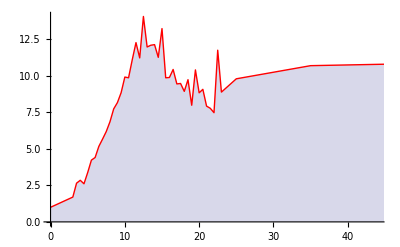

```mathematica
lp = ListPlot[val,Joined->True, PlotStyle->Red, Filling->Axis]
```

```mathematica
curve = Fit[val,{1, x,x^2, x^3, x^4, x^5, x^6, x^7,Exp[x]}, x]
```

1.65959+8.66302×10^-27 ⅇ^x-2.21431 x+0.871924 x^2-0.0909011 x^3+0.00436892 x^4-0.000108096 x^5+1.3384×10^-6 x^6-6.57234×10^-9 x^7

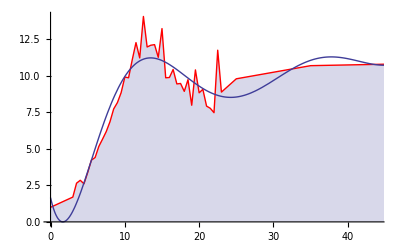

```mathematica
Show[lp, Plot[curve,{x,0.0,90.0}]]
```